```mathematica
D[ρ, t] + D[(ρ v), x] = (Subscript[k, A](1-ϕ) + Subscript[k, B] ϕ)ρ
D[ϕ, t]  + v D[ϕ, x] = D (∂_x)^2 ϕ+ D(D[ρ, x] D[ϕ, t])/ρ + (Subscript[k, B]-Subscript[k, A]+Subscript[k, F])ϕ(1-ϕ) + Subscript[k, D](1-ϕ) 
η(∂_x)^2 v - ξ v =  E D[ρ, x]/ρ+ D[E, x] log(ρ/Subscript[ρ, h]) 

Where
E = Subscript[E, M] (1-ϕ) + Subscript[E, O] ϕ
kA:= 1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
kD := α E;
```

```mathematica
Clear["Global`*"]
```

## Initial conditions

### Sigmoid function

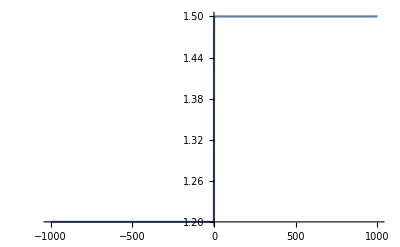

```mathematica
(*Initial conditions*)
Plot[ (Tanh[8 x]+1)/2 (ρdA-ρdB)+ρdB/.{ρdA->1.5, ρdB-> 1.2}  , {x, -L, L}]
```

```mathematica
iv
```

{ρ[x,0]==1,ϕ[x,0]==1/2 (1-Tanh[x/125]),v[x,0]==0}

```mathematica
Tanh[10]//N
```

1.

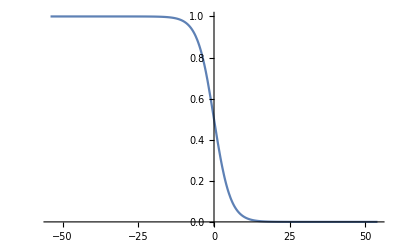

```mathematica
a=10;
Plot[1/2 (1-Tanh[a (x)/L]), {x, -L, L}]
```

### Import from data

```mathematica
fname = "/Users/dang/Documents/Projects/Tabler_skull/Figures/Live_imaging_intensity_profiles/smoothened_profile_video_1_scaled_intensities.xlsx";
s=Import[fname, "Data"] ;

npoints=Dimensions[s[[1]]][[-1]]-1;
```

```mathematica
dataIn=Import[fname,{"Data",1,2;;3,Range[2, npoints] }];
Print[dataIn // Dimensions]
dataIn[[;;, ;;10]]
```

{2,3741}

{{-400.,-399.773,-399.545,-399.318,-399.091,-398.864,-398.636,-398.409,-398.182,-397.955},{0.903629,0.903629,0.903629,0.903629,0.903629,0.903629,0.903629,0.903629,0.903629,0.903629}}

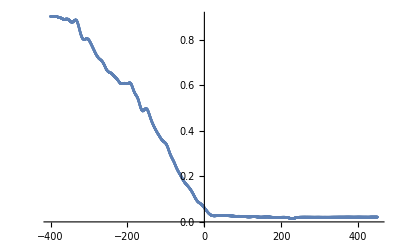

```mathematica
dataT=Transpose[dataIn];
ListPlot[dataT]
```

```mathematica
firstPoint=dataIn[[2, 1]];
lastPoint=dataIn[[2, -1]];
PrependTo[dataT, {-500, firstPoint}];
AppendTo[dataT, {500, lastPoint}];
```

```mathematica
fData=Interpolation[dataT]
```

InterpolatingFunction[…]

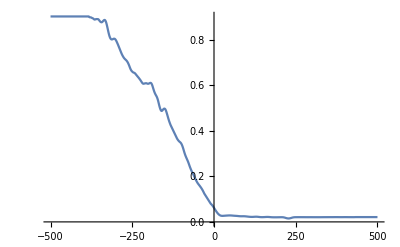

```mathematica
Plot[fData[x], {x, -500, 500}]
```

## Code from stackexchange

-1 < -kap < 1

```mathematica
params={kA->.1,kB->1,D1->.1,η->1,ξ->1,kD->1,kF->.5,z->1, kap->-1};rh0=1;tmax=1;L=1;iv={ρ[x,0]==rh0,ϕ[x,0]==(1-Tanh[8 x])/2,v[x,0]==0};bc={ρ[-L,t]==rh0,ρ[L,t]==rh0,ϕ[-L,t]==(1+Tanh[8 L])/2,ϕ[L,t]==(1-Tanh[8 L])/2,v[-L,t]==0,v[L,t]==0};

PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+z D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA+kF) ϕ[x,t] (1-ϕ[x,t])+kD, ρ[x,t](η D[v[x,t],{x,2}]-ξ v[x,t])==(1+kap ϕ[x,t]) D[ρ[x,t],x]};
vars={ρ,ϕ,v}
fullsys=Join[PDEsys/.params,bc,iv];

ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}]
```

{ρ,ϕ,v}

NDSolve::eerr: Warning: scaled local spatial error estimate of 13.617 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 89 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{ρ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
{Plot3D[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",AxesLabel->Automatic,PlotLabel->"ρ"],Plot3D[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",AxesLabel->Automatic,PlotLabel->"ϕ"],Plot3D[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",AxesLabel->Automatic,PlotLabel->"v"]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Solve model

#### Parameters

```mathematica
(*Random parameters *)
(*params={ρdA->1, ρdB->1, τ-> 1, D1->.1, η->1, ξ->1, kF->0, z->1, α->1, eM->0.5,eO->1}; *)params={ρdA->1.1, ρdB->1.1, ρh-> 1.2, τ->0.1, D1->0.01, η->0.1, ξ->0.1, kF->1,z->1, α->2, eM->0.1, eO->1}; 
params={eM->0.1, eO->1,η->0.1, ξ->0.1,τ->0.1, D1->0.01,  α->2,  ρdA->1.1, ρdB->1.1, ρh-> 1.2 };
L=1;
tmax=1;
```

Parameter estimates
	eO ~ 1000 Pa (AFM) - maybe MegaPascal?
	eM ~ 30 Pa  (AFM)
	η ~ 10^4 Pa s ~ 25/9Pa hr 						
	ξ ~ 10^(3) Pa μm^-2 s = 10^(9) Pa mm^-2 s = 5/18 Pa μm^-2 hr   
	τ ~ 12 hr = 43200 s (cell division time)
	D ~  1 μm^2/s =  10^-6  mm^2/s ~ 3600 μm^2/hr (related to MSD of cell after subtracting motion)
	α ~  kD/e ~ 1 /(10 hr) / 100 Pa =  1 / ( 1000 Pa hr) = 1/(360000) s^-1 Pa^-1 

Sizes
	L ~ 1000 μm = 1mm (microscopy image)
	(ρ^h)_M (mesenchyme) ~ 1 cell / (10 μm)^2 = 0.01 μm^-2  ~ 1 / (0.01 mm)^2 ~ 10^4 mm^-2
	(ρ^h)_O (osteoblast) ~ 1 cell / (100 μm^2) ~ 10^4 mm^-2
	
“Free estimates”
	ρ^H ~  (sets density at which P=0)

```mathematica
(*Saved parameters*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  (* higher a = steeper Tanh function *)
L=1000;
tmax=5;
```

```mathematica
(*time in s, length in mm*) 
(*
params = {eO-> 1000, eM-> 30, η-> 10^4, ξ-> 10^9, τ-> 3600, D1-> 10^(-6), α-> 36, ρdA-> 10^4, ρdB-> 10^4}; 
L=1;
tmax=1000;
*)
(*time in hr, length in μm*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  (* higher a = steeper Tanh function *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->3600, α-> 1/100, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh-> 1/2*10^(-2)};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 1, D1->1, α-> 1/100, ρdA-> 10^(0), ρdB-> 10^(0), ρh-> 10^(0)};*)
L=500; (* consistent with input data!*)
tmax=6;
```

```mathematica
kA:= 1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) ; (* Stiffness *)  
kD := α (e-eM);
```

#### Try solving for v[x, t=0]

```mathematica
(*Try solving for v[x, t=0] *)
pde=(ρ0[x](η D[v0[x],{x,2}]-ξ v0[x])==e D[ρ0[x],x] +(eO -eM )D[ϕ0[x],x]Log[ρ0[x]/ρh]*ρ0[x] )/. params;
v0sol=NDSolve[ {pde, v0[-L]==0, v0[L]==0}, v0[x], {x, -L, L}, InterpolationOrder->All, PrecisionGoal->10];
Plot[v0[x] /. v0sol, {x, -L, L}]
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 5.06675×10^258 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

-Graphics-

#### Boundary and initial conditions

Boundary conditions and initial conditions need to be consistent!

```mathematica
(*ρ0[x_]:=(Tanh[a (x+0.L)/L]+1)/2 (ρdA-ρdB)+ ρdB
ϕ0[x_]:=(1-Tanh[a(x+0.L)/L])/2;*)
ρ0[x_]:=(Tanh[a x/L]+1)/2 (ρdA-ρdB)+ ρdB
ϕ0[x_]:=(1-Tanh[a x/L])/2;
(*iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;*)
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==fData[x],v[x,0]==0} /. params;
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
(*bc={ρ[-L,t]==(Tanh[-8 L]+1)/2 (ρdA-ρdB)+ ρdB,ρ[L,t]==(Tanh[8 L]+1)/2 (ρdA-ρdB)+ ρdB,ϕ[-L,t]==(1+Tanh[8 L])/2,ϕ[L,t]==(1-Tanh[8 L])/2,v[-L,t]==0,v[L,t]==0} /. params;*)
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-ξ v[x,t])==e D[ρ[x,t],x] + D[e, x] Log[ρ[x,t]/ρh]*ρ[x,t]};
vars={ρ,ϕ,v}
fullsys=Simplify@Join[PDEsys/.params,bc,iv];

(*ndsol= NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->Automatic]*)
ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}, InterpolationOrder->All, PrecisionGoal-> Infinity, MaxStepSize->30] (*, MaxSteps->100000, MaxStepSize->1] *)
(*ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}, PrecisionGoal->Infinity, InterpolationOrder->All]*)
```

{ρ,ϕ,v}

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

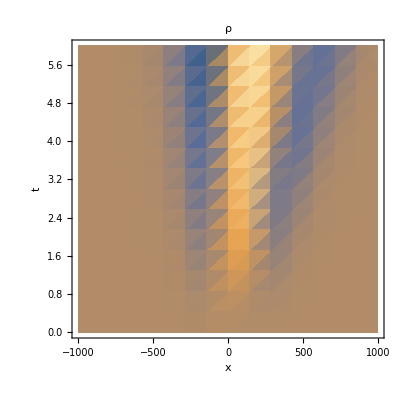
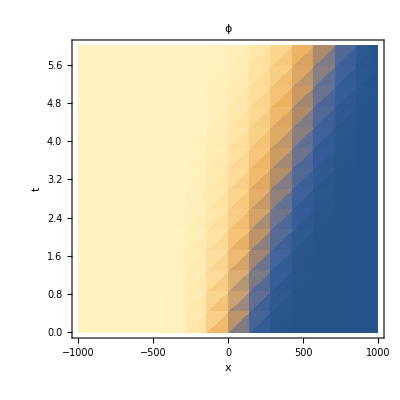
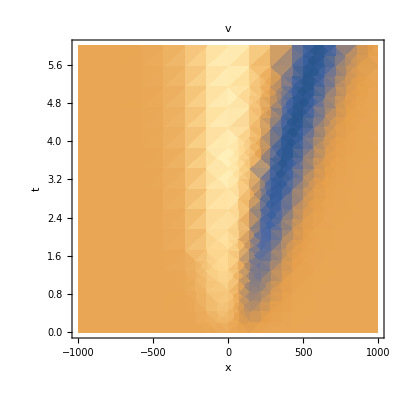

```mathematica
{DensityPlot[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLabel->"ρ"],
DensityPlot[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLabel->"ϕ"],
DensityPlot[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLabel->"v"]}
```

```mathematica
{Plot3D[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",PlotRange-> All,AxesLabel->Automatic,PlotLabel->"ρ"],Plot3D[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",PlotRange-> All,AxesLabel->Automatic,PlotLabel->"ϕ"],Plot3D[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",PlotRange-> All,AxesLabel->Automatic,PlotLabel->"v"]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Simplify/@fullsys // TableForm
```

## Solve easier model

```mathematica
D[ϕ, t]  + v D[ϕ, x] = D (∂_x)^2 ϕ + (Subscript[k, B]-Subscript[k, A])ϕ(1-ϕ) + Subscript[k, D](1-ϕ) 
η(∂_x)^2 v - ξ v =  D[E, x] log(ρ/Subscript[ρ, h]) 

Where
E = Subscript[E, M] (1-ϕ) + Subscript[E, O] ϕ
kA:= 1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
kD := α E;
```

```mathematica
params={ρdA->1.2, ρdB->1.1, ρh-> 1.2, τ->0.1, D1->0.01, η->0.1, ξ->0.1, kF->1,z->1, α->2, eM->0.1, eO->1, kD-> 0, a-> 8}; 
L=1; (* consistent with input data!*)
tmax=1;
```

```mathematica
kA:= 1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) ; (* Stiffness *)  
(* kD := α (e-eM); *)
```

```mathematica
ϕ0[x_]:=(1-Tanh[a x/L])/2;
iv={ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
bc={ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
PDEsys={D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
(η D[v[x,t],{x,2}]-ξ v[x,t])== 0};
vars={ϕ,v};
fullsys=Simplify@Join[PDEsys/.params,bc,iv]
```

{ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==0.+ρ[x,t] (-0.757576+0.757576 ϕ[x,t]) ϕ[x,t]+0.01 ϕ^(2,0)[x,t],1. v[x,t]==1. v^(2,0)[x,t],2 ϕ[-1,t]==1+Tanh[8],(1+ⅇ^16) ϕ[1,t]==1,v[-1,t]==0,v[1,t]==0,Tanh[8 x]+2 ϕ[x,0]==1,v[x,0]==0}

```mathematica
ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}] (* [InterpolationOrder->All, PrecisionGoal-> Infinity, MaxStepSize->30, MaxSteps->100000, MaxStepSize->1] *)
```

NDSolve::underdet: There are more dependent variables, {v[x,t],ρ[x,t],ϕ[x,t]}, than equations, so the system is underdetermined.

NDSolve[{ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==0.+ρ[x,t] (-0.757576+0.757576 ϕ[x,t]) ϕ[x,t]+0.01 ϕ^(2,0)[x,t],1. v[x,t]==1. v^(2,0)[x,t],2 ϕ[-1,t]==1+Tanh[8],(1+ⅇ^16) ϕ[1,t]==1,v[-1,t]==0,v[1,t]==0,Tanh[8 x]+2 ϕ[x,0]==1,v[x,0]==0},{ϕ,v},{x,-1,1},{t,0,1},Method→{EquationSimplification→Residual,IndexReduction→Automatic}]

```mathematica
{Plot3D[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",PlotRange-> All,AxesLabel->Automatic,PlotLabel->"ϕ"],Plot3D[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,ColorFunction->"Rainbow",PlotRange-> All,AxesLabel->Automatic,PlotLabel->"v"]}
```

{-Graphics3D-,-Graphics3D-}